```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mouze\Desktop\CM_labs\lab9\lab9\lab9

```mathematica
num = Import["var1.txt","Table"]
```

{{0,0.00983912,0.0392798,0.0871421,0.151512,0.229816,0.318928,0.415287,0.515048,0.614225,0.708859,0.795171,0.869715,0.929511,0.97217,0.995985,1},{0.1,0.109839,0.13928,0.187142,0.251512,0.329817,0.418928,0.515288,0.615048,0.714225,0.808859,0.895172,0.969715,1.02951,1.07217,1.09598,1.1},{0.2,0.209839,0.23928,0.287143,0.351512,0.429817,0.518929,0.615288,0.715048,0.814226,0.90886,0.995172,1.06972,1.12951,1.17217,1.19598,1.2},{0.3,0.309839,0.33928,0.387143,0.451512,0.529817,0.618929,0.715288,0.815049,0.914226,1.00886,1.09517,1.16972,1.22951,1.27217,1.29598,1.3},{0.4,0.409839,0.43928,0.487143,0.551513,0.629817,0.718929,0.815289,0.915049,1.01423,1.10886,1.19517,1.26972,1.32951,1.37217,1.39598,1.4},{0.5,0.509839,0.53928,0.587143,0.651513,0.729817,0.818929,0.915289,1.01505,1.11423,1.20886,1.29517,1.36972,1.42951,1.47217,1.49598,1.5},{0.6,0.609839,0.63928,0.687143,0.751513,0.829817,0.918929,1.01529,1.11505,1.21423,1.30886,1.39517,1.46972,1.52951,1.57217,1.59598,1.6},{0.7,0.709839,0.73928,0.787143,0.851512,0.929817,1.01893,1.11529,1.21505,1.31423,1.40886,1.49517,1.56972,1.62951,1.67217,1.69598,1.7},{0.8,0.809839,0.83928,0.887143,0.951512,1.02982,1.11893,1.21529,1.31505,1.41423,1.50886,1.59517,1.66972,1.72951,1.77217,1.79598,1.8},{0.9,0.909839,0.93928,0.987142,1.05151,1.12982,1.21893,1.31529,1.41505,1.51423,1.60886,1.69517,1.76971,1.82951,1.87217,1.89598,1.9},{1,1.00984,1.03928,1.08714,1.15151,1.22982,1.31893,1.41529,1.51505,1.61422,1.70886,1.79517,1.86971,1.92951,1.97217,1.99598,2}}

```mathematica
true = Table[(i*0.1)^2+(j*0.1)^2,{i,0,1/0.1},{j,0,1/0.1}] //Transpose
```

{{0.,0.01,0.04,0.09,0.16,0.25,0.36,0.49,0.64,0.81,1.},{0.01,0.02,0.05,0.1,0.17,0.26,0.37,0.5,0.65,0.82,1.01},{0.04,0.05,0.08,0.13,0.2,0.29,0.4,0.53,0.68,0.85,1.04},{0.09,0.1,0.13,0.18,0.25,0.34,0.45,0.58,0.73,0.9,1.09},{0.16,0.17,0.2,0.25,0.32,0.41,0.52,0.65,0.8,0.97,1.16},{0.25,0.26,0.29,0.34,0.41,0.5,0.61,0.74,0.89,1.06,1.25},{0.36,0.37,0.4,0.45,0.52,0.61,0.72,0.85,1.,1.17,1.36},{0.49,0.5,0.53,0.58,0.65,0.74,0.85,0.98,1.13,1.3,1.49},{0.64,0.65,0.68,0.73,0.8,0.89,1.,1.13,1.28,1.45,1.64},{0.81,0.82,0.85,0.9,0.97,1.06,1.17,1.3,1.45,1.62,1.81},{1.,1.01,1.04,1.09,1.16,1.25,1.36,1.49,1.64,1.81,2.}}

```mathematica
ListContourPlot[num-true]
```

Thread::tdlen: Objects of unequal length in {0,0.00983912,0.0392798,0.0871421,0.151512,0.229816,0.318928,0.415287,0.515048,0.614225,«7»}+{0.,-0.01,-0.04,-0.09,«3»,-0.49,-0.64,-0.81,«1»} cannot be combined.

Thread::tdlen: Objects of unequal length in {0.1,0.109839,0.13928,0.187142,0.251512,0.329817,0.418928,0.515288,0.615048,0.714225,«7»}+{-0.01,-0.02,-0.05,«5»,-0.65,-0.82,«1»} cannot be combined.

Thread::tdlen: Objects of unequal length in {0.2,0.209839,0.23928,0.287143,0.351512,0.429817,0.518929,0.615288,0.715048,0.814226,«7»}+{-0.04,-0.05,-0.08,«5»,-0.68,-0.85,«1»} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

ListContourPlot::arrayerr: {{0.,-0.01,-0.04,-0.09,-0.16,-0.25,-0.36,-0.49,-0.64,-0.81,«1»}+{0,0.00983912,0.0392798,«5»,0.515048,0.614225,«7»},«9»,«1»} must be a valid array.

ListContourPlot[{{0.,-0.01,-0.04,-0.09,-0.16,-0.25,-0.36,-0.49,-0.64,-0.81,-1.}+{0,0.00983912,0.0392798,0.0871421,0.151512,0.229816,0.318928,0.415287,0.515048,0.614225,0.708859,0.795171,0.869715,0.929511,0.97217,0.995985,1},{-0.01,-0.02,-0.05,-0.1,-0.17,-0.26,-0.37,-0.5,-0.65,-0.82,-1.01}+{0.1,0.109839,0.13928,0.187142,0.251512,0.329817,0.418928,0.515288,0.615048,0.714225,0.808859,0.895172,0.969715,1.02951,1.07217,1.09598,1.1},{-0.04,-0.05,-0.08,-0.13,-0.2,-0.29,-0.4,-0.53,-0.68,-0.85,-1.04}+{0.2,0.209839,0.23928,0.287143,0.351512,0.429817,0.518929,0.615288,0.715048,0.814226,0.90886,0.995172,1.06972,1.12951,1.17217,1.19598,1.2},{-0.09,-0.1,-0.13,-0.18,-0.25,-0.34,-0.45,-0.58,-0.73,-0.9,-1.09}+{0.3,0.309839,0.33928,0.387143,0.451512,0.529817,0.618929,0.715288,0.815049,0.914226,1.00886,1.09517,1.16972,1.22951,1.27217,1.29598,1.3},{-0.16,-0.17,-0.2,-0.25,-0.32,-0.41,-0.52,-0.65,-0.8,-0.97,-1.16}+{0.4,0.409839,0.43928,0.487143,0.551513,0.629817,0.718929,0.815289,0.915049,1.01423,1.10886,1.19517,1.26972,1.32951,1.37217,1.39598,1.4},{-0.25,-0.26,-0.29,-0.34,-0.41,-0.5,-0.61,-0.74,-0.89,-1.06,-1.25}+{0.5,0.509839,0.53928,0.587143,0.651513,0.729817,0.818929,0.915289,1.01505,1.11423,1.20886,1.29517,1.36972,1.42951,1.47217,1.49598,1.5},{-0.36,-0.37,-0.4,-0.45,-0.52,-0.61,-0.72,-0.85,-1.,-1.17,-1.36}+{0.6,0.609839,0.63928,0.687143,0.751513,0.829817,0.918929,1.01529,1.11505,1.21423,1.30886,1.39517,1.46972,1.52951,1.57217,1.59598,1.6},{-0.49,-0.5,-0.53,-0.58,-0.65,-0.74,-0.85,-0.98,-1.13,-1.3,-1.49}+{0.7,0.709839,0.73928,0.787143,0.851512,0.929817,1.01893,1.11529,1.21505,1.31423,1.40886,1.49517,1.56972,1.62951,1.67217,1.69598,1.7},{-0.64,-0.65,-0.68,-0.73,-0.8,-0.89,-1.,-1.13,-1.28,-1.45,-1.64}+{0.8,0.809839,0.83928,0.887143,0.951512,1.02982,1.11893,1.21529,1.31505,1.41423,1.50886,1.59517,1.66972,1.72951,1.77217,1.79598,1.8},{-0.81,-0.82,-0.85,-0.9,-0.97,-1.06,-1.17,-1.3,-1.45,-1.62,-1.81}+{0.9,0.909839,0.93928,0.987142,1.05151,1.12982,1.21893,1.31529,1.41505,1.51423,1.60886,1.69517,1.76971,1.82951,1.87217,1.89598,1.9},{-1.,-1.01,-1.04,-1.09,-1.16,-1.25,-1.36,-1.49,-1.64,-1.81,-2.}+{1,1.00984,1.03928,1.08714,1.15151,1.22982,1.31893,1.41529,1.51505,1.61422,1.70886,1.79517,1.86971,1.92951,1.97217,1.99598,2}}]

```mathematica
g = Show[ListPlot3D[num],ImageSize->600]
```

-Graphics3D-

```mathematica
ListContourPlot3D[true]
```

Visualization`Core`ListContourPlot3D::gmat1: Data value {{0.,0.01,0.04,0.09,0.16,0.25,0.36,0.49,0.64,0.81,«1»},«9»,«1»} must be a list of points of dimension 3.

ListContourPlot3D[{{0.,0.01,0.04,0.09,0.16,0.25,0.36,0.49,0.64,0.81,1.},{0.01,0.02,0.05,0.1,0.17,0.26,0.37,0.5,0.65,0.82,1.01},{0.04,0.05,0.08,0.13,0.2,0.29,0.4,0.53,0.68,0.85,1.04},{0.09,0.1,0.13,0.18,0.25,0.34,0.45,0.58,0.73,0.9,1.09},{0.16,0.17,0.2,0.25,0.32,0.41,0.52,0.65,0.8,0.97,1.16},{0.25,0.26,0.29,0.34,0.41,0.5,0.61,0.74,0.89,1.06,1.25},{0.36,0.37,0.4,0.45,0.52,0.61,0.72,0.85,1.,1.17,1.36},{0.49,0.5,0.53,0.58,0.65,0.74,0.85,0.98,1.13,1.3,1.49},{0.64,0.65,0.68,0.73,0.8,0.89,1.,1.13,1.28,1.45,1.64},{0.81,0.82,0.85,0.9,0.97,1.06,1.17,1.3,1.45,1.62,1.81},{1.,1.01,1.04,1.09,1.16,1.25,1.36,1.49,1.64,1.81,2.}}]

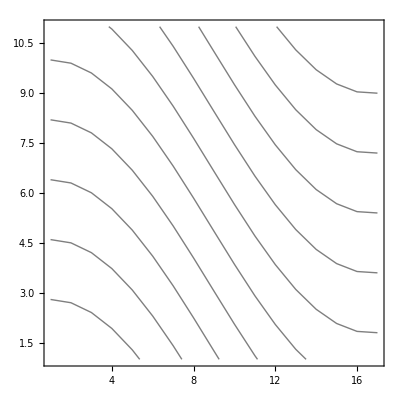

```mathematica
g=Show[ListContourPlot[num,ContourShading->None,Contours->10]]
```

```mathematica
Export["var1_2.png",g]
```

var1_2.png